## PrunedDelaunay-example.nb PrunedDelaunayEdges, PrunedDelaunayPairs

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (2.3.6 (10-Nov-2012)) loaded Sat 10 Nov 2012 14:51:31
using xCellerator 0.90 and XSSA 1204002
GPL License Terms Apply

Here is a list of points

```mathematica
v={{1.027931720725517,1.301965492108515},{2.202218860706698,3.2257349251632697},{1.035415670561728,5.655997595984954},{2.386904318481222,7.109317592362457},{1.0833751709794355,8.980482308933432},{3.502270732345678,1.335254274584683},{4.361093707901039,3.6485709673028204},{3.196894279960989,5.534526287179236},{4.095796640417647,7.674424268506447},{2.9003660026449554,9.251835936434572},{5.722830056052847,0.8617764462583238},{6.80773012022238,3.485761589627591},{5.526263297034821,5.189734664555409},{6.187223958272119,7.521726508513439},{5.129537710249264,9.231984081618066},{7.219127605846668,1.6157536127840533},{8.806178313487068,3.415390299008257},{7.271042098221217,5.711781963929349},{8.611971844838648,7.23689487373882},{7.292525547259082,9.037955358764131},{9.19271138063058,1.096774038890791},{0.7249110136647698,3.966777672550985},{9.260846224641924,5.442715323747296},{0.7296041122054311,7.311337194587003},{9.121140466586665,9.09535112712043}};
```

Find the Delaunay Triangulation of the points

```mathematica
de=DelaunayEdges[v]
```

{{{1.02793,1.30197},{2.20222,3.22573}},{{1.02793,1.30197},{3.50227,1.33525}},{{1.02793,1.30197},{5.72283,0.861776}},{{1.02793,1.30197},{0.724911,3.96678}},{{2.20222,3.22573},{1.03542,5.656}},{{2.20222,3.22573},{3.50227,1.33525}},{{2.20222,3.22573},{4.36109,3.64857}},{{2.20222,3.22573},{3.19689,5.53453}},{{2.20222,3.22573},{0.724911,3.96678}},{{1.03542,5.656},{2.3869,7.10932}},{{1.03542,5.656},{3.19689,5.53453}},{{1.03542,5.656},{0.724911,3.96678}},{{1.03542,5.656},{0.729604,7.31134}},{{2.3869,7.10932},{1.08338,8.98048}},{{2.3869,7.10932},{3.19689,5.53453}},{{2.3869,7.10932},{4.0958,7.67442}},{{2.3869,7.10932},{2.90037,9.25184}},{{2.3869,7.10932},{0.729604,7.31134}},{{1.08338,8.98048},{2.90037,9.25184}},{{1.08338,8.98048},{0.729604,7.31134}},{{3.50227,1.33525},{4.36109,3.64857}},{{3.50227,1.33525},{5.72283,0.861776}},{{4.36109,3.64857},{3.19689,5.53453}},{{4.36109,3.64857},{5.72283,0.861776}},{{4.36109,3.64857},{6.80773,3.48576}},{{4.36109,3.64857},{5.52626,5.18973}},{{3.19689,5.53453},{4.0958,7.67442}},{{3.19689,5.53453},{5.52626,5.18973}},{{4.0958,7.67442},{2.90037,9.25184}},{{4.0958,7.67442},{5.52626,5.18973}},{{4.0958,7.67442},{6.18722,7.52173}},{{4.0958,7.67442},{5.12954,9.23198}},{{2.90037,9.25184},{5.12954,9.23198}},{{5.72283,0.861776},{6.80773,3.48576}},{{5.72283,0.861776},{7.21913,1.61575}},{{5.72283,0.861776},{9.19271,1.09677}},{{6.80773,3.48576},{5.52626,5.18973}},{{6.80773,3.48576},{7.21913,1.61575}},{{6.80773,3.48576},{8.80618,3.41539}},{{6.80773,3.48576},{7.27104,5.71178}},{{5.52626,5.18973},{6.18722,7.52173}},{{5.52626,5.18973},{7.27104,5.71178}},{{6.18722,7.52173},{5.12954,9.23198}},{{6.18722,7.52173},{7.27104,5.71178}},{{6.18722,7.52173},{8.61197,7.23689}},{{6.18722,7.52173},{7.29253,9.03796}},{{5.12954,9.23198},{7.29253,9.03796}},{{5.12954,9.23198},{9.12114,9.09535}},{{7.21913,1.61575},{8.80618,3.41539}},{{7.21913,1.61575},{9.19271,1.09677}},{{8.80618,3.41539},{7.27104,5.71178}},{{8.80618,3.41539},{9.19271,1.09677}},{{8.80618,3.41539},{9.26085,5.44272}},{{7.27104,5.71178},{8.61197,7.23689}},{{7.27104,5.71178},{9.26085,5.44272}},{{8.61197,7.23689},{7.29253,9.03796}},{{8.61197,7.23689},{9.26085,5.44272}},{{8.61197,7.23689},{9.12114,9.09535}},{{7.29253,9.03796},{9.12114,9.09535}},{{9.19271,1.09677},{9.26085,5.44272}},{{0.724911,3.96678},{0.729604,7.31134}},{{9.26085,5.44272},{9.12114,9.09535}}}

Plot the Delaunay Triangulation

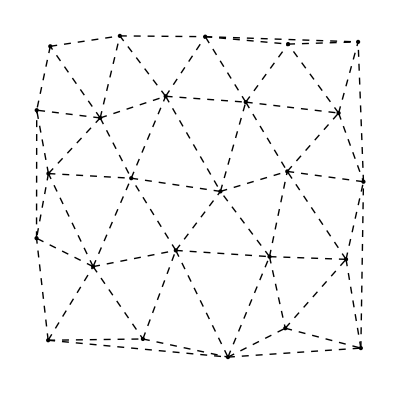

```mathematica
deplot=Graphics[Join[Point/@v, {Dashed}, Line/@de]]
```

Find the Bounded Voronoi

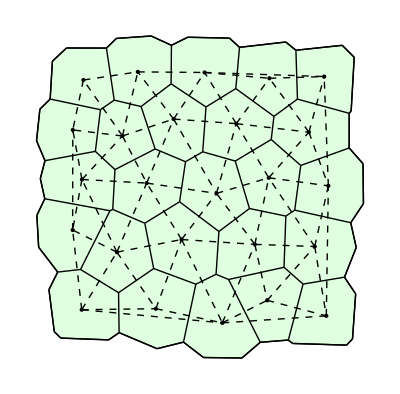

```mathematica
Show[ShowTissue[BoundedCellVoronoi[v]],deplot]
```

Compare the Pruned Delaunay (Red) with the Full Delaunay (Black Dashes)

```mathematica
pde=PrunedDelaunayEdges[v];
```

```mathematica
pdeplot=Graphics[{Thick,Pink, Line/@pde}];
```

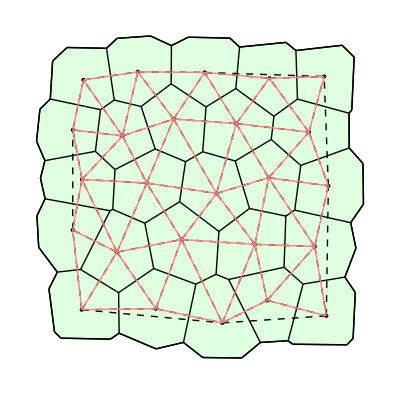

```mathematica
Show[ShowTissue[BoundedCellVoronoi[v]],deplot, pdeplot]
```

```mathematica
PrunedDelaunayPairs[v]
```

{{1,2},{1,6},{1,22},{2,3},{2,6},{2,7},{2,8},{2,22},{3,4},{3,8},{3,22},{3,24},{4,5},{4,8},{4,9},{4,10},{4,24},{5,10},{5,24},{6,7},{6,11},{7,8},{7,11},{7,12},{7,13},{8,9},{8,13},{9,10},{9,13},{9,14},{9,15},{10,15},{11,12},{11,16},{12,13},{12,16},{12,17},{12,18},{13,14},{13,18},{14,15},{14,18},{14,19},{14,20},{15,20},{16,17},{16,21},{17,18},{17,21},{17,23},{18,19},{18,23},{19,20},{19,23},{19,25},{20,25}}

```mathematica
DelaunayPairs[v]
```

{{1,2},{1,6},{1,11},{1,22},{2,3},{2,6},{2,7},{2,8},{2,22},{3,4},{3,8},{3,22},{3,24},{4,5},{4,8},{4,9},{4,10},{4,24},{5,10},{5,24},{6,7},{6,11},{7,8},{7,11},{7,12},{7,13},{8,9},{8,13},{9,10},{9,13},{9,14},{9,15},{10,15},{11,12},{11,16},{11,21},{12,13},{12,16},{12,17},{12,18},{13,14},{13,18},{14,15},{14,18},{14,19},{14,20},{15,20},{15,25},{16,17},{16,21},{17,18},{17,21},{17,23},{18,19},{18,23},{19,20},{19,23},{19,25},{20,25},{21,23},{22,24},{23,25}}

```mathematica
Complement[DelaunayPairs[v], PrunedDelaunayPairs[v]]
```

{{1,11},{11,21},{15,25},{21,23},{22,24},{23,25}}